## Exercises Lab 1, Jeroen Hofman 10194754

### Exercise 1: Bacteria Growth

Bacteria are inoculated in a petri dish at a density of 10/ml. The bacerial density doubles in twenty hours. Assume that this situation is described by the differential equation
       dx/dt = C x
where x is the bacterial density and C is a constant.
(i) Integrate this equation giving x as a function of time and find the value of C.
(ii) How long does it take for the density to increase to eight times its original value? To ten times?

#### Solution

Solving the differential equation:

```mathematica
solx =DSolve[{x'[t]==C x[t],x[0]==10},x[t],t]
```

{{x[t]→10 ⅇ^(C t)}}

Solving for C:

```mathematica
solC = Solve[(2x[t]/.solx/.t->0)==(x[t]/.solx/.t->20),C]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{C→Log[2]/20}}

Eight times the original value:

```mathematica
Solve[(x[t]/.solx/.solC)==(8 x[t]/.solx/.solC/.t->0),t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→60}}

Ten times the original value:

```mathematica
Solve[(x[t]/.solx/.solC)==(10 x[t]/.solx/.solC/.t->0),t]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→66.4386}}

### Exercise 2: Growth Model ( Linear vs. Exponential )

Are the following data better described by linear growth or exponential growth ?  Write down the differential equation for this data set and complete with numerical values for the parameters (Hint : using Mathematica function Fit or  FindFit).
t                        x                                            t                           x
0.5                  1.27                                        1.6                      18.45
0.6                  6.58                                        1.7                      19.85
0.7                  7.00                                        1.8                      25.03
0.8                  8.83                                        1.9                      28.14
0.9                  8.66                                        2.0                      28.31
1.0                  5.53                                        2.1                      33.41
1.1                  9.33                                        2.2                      41.43
1.2                 14.57                                       2.3                      40.87
1.3                  8.51                                        2.4                      56.71
1.4                17.61                                        2.5                      59.32
1.5                 12.94

#### Solution

{a→1.48353,b→1.70259,c→1.41534}

{a→-15.9278,b→24.9788}

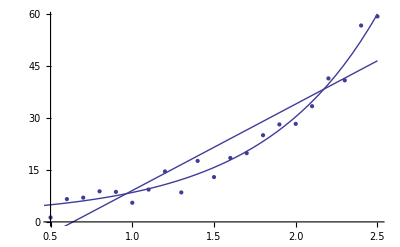

```mathematica
data = {{0.5,1.27},{0.6,6.58},{0.7,7.00},{0.8,8.83},{0.9,8.66},{1.0,5.53},{1.1,9.33},{1.2,14.57},{1.3,8.51},{1.4,17.61},
{1.5,12.94},{1.6,18.45},{1.7,19.85},{1.8,25.03},{1.9,28.14},{2.0,28.31},{2.1,33.41},{2.2,41.43},{2.3,40.87},{2.4,56.71},
{2.5,59.32}};
expFit = FindFit[data,a + b Exp[c x],{a,b,c},x]
linFit = FindFit[data,a + b x,{a,b},x]
Show[ListPlot[data],Plot[a + b Exp[c x]/.expFit,{x,0,2.5}],Plot[a + b x/.linFit,{x,0,2.5}]]
```

### Exercise 3: Population Dynamics

A theoretical ecologist is examining mathematical models for population dynamics. She considers the equation
       dx/dt=f(x)=(2 x^m)/(1+x^4)-x,  x≥0,
where x is the population density and m is a positive integer. 
(i). For m=1, sketch f(x) and determine the number and stability of all fixed points. Describe the dynamics as t→∞ for initial conditions of very small positive densities (say, x(0)=0.01) and very large positive densities (say, x(0)=100), respectively.
(ii). For m=2, sketch f(x) and determine the number and stability of all fixed points. Describe the dynamics as t→∞ for initial conditions of very small positive densities (say, x(0)=0.01) and very large positive densities (say, x(0)=100), respectively and make comparison with (i).

#### Solution

Fixed points and stability

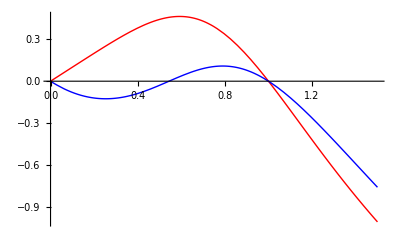

{{x→-1},{x→0},{x→1}}

{-2,1,-2}

{{x→0.},{x→0.543689},{x→1.}}

{-1.,0.678574,-1.}

```mathematica
f[x_] = 2 x^m/(1 + x^4)-x;
Show[Plot[f[x]/.{m->1},{x,0,1.5},PlotRange->All,PlotStyle->Red],Plot[f[x]/.{m->2},{x,0,1.5},PlotRange->All,PlotStyle->Blue]]
roots = Solve[(f[x]/.{m->1})==0,x,Reals]
f'[x]/.m->1/.roots
roots = NSolve[(f[x]/.{m->2})==0,x,Reals]
f'[x]/.m->2/.roots
```

Dynamics

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

General::stop: Further output of DSolve :: bvnul will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

General::stop: Further output of DSolve :: bvnul will be suppressed during this calculation.

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

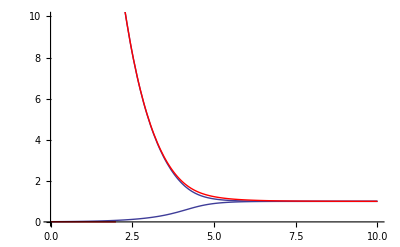

```mathematica
fitSmall = DSolve[{{x'[t]==((2 x[t]^m/(1 + x[t]^4))-x[t])/.m->1},{x[0]==0.01}},x[t],t];
fitLarge= DSolve[{{x'[t]==((2 x[t]^m/(1 + x[t]^4))-x[t])/.m->1},{x[0]==100}},x[t],t];
fitSmall2 = NDSolve[{{x'[t]==((2 x[t]^m/(1 + x[t]^4))-x[t])/.m->2.},{x[0]==0.01}},x[t],{t,0,10}]
fitLarge2= NDSolve[{{x'[t]==((2 x[t]^m/(1 + x[t]^4))-x[t])/.m->2.},{x[0]==100}},x[t],{t,0,10}];
Show[Plot[x[t]/.Flatten[fitSmall][[1]],{t,0,10},PlotRange->{{0,10},{0,10}}],Plot[x[t]/.Flatten[fitLarge][[1]],{t,0,10}],
Plot[Evaluate[x[t]/.fitSmall2],{t,0,2},PlotStyle->Red],Plot[Evaluate[x[t]/.fitLarge2],{t,0,10},PlotStyle->Red]]
```

### Exercise 4: Finite Difference Equation for Periodic Stimulation

The finite-difference equation 
      ϕ_(t+1)= 0.5 + α sin (2π ϕ_t),  0≤ ϕ_t ≤1,
 where 0≤α<0.5,  has been used as a mathematical model for periodic stimulation of biological oscillators.
 (i) Determine the steady state and its stability as a function of α.
 (ii) Sketch  ϕ_(t+1) as a function of  ϕ_t for α=0.25. Be sure to indicate all maxima, minima and inflection points.
 (iii) For α=0.25 there is a stable period-2 orbit ( for a given map y_(t+1)=f(y_t), it has a stable period-2 orbit means that  y_(t+2)=f(f(y_t))= y_t and at the same time y_(t+1)=f(y_t)≠y_t ). What is it?

#### Solution

```mathematica
ClearAll["Global`*"];
f[ϕ_] = 0.5 + α Sin[2π ϕ];
sola=FindRoot[(f[ϕ]/.α->0.0)-ϕ,{ϕ,0.5}]
sola=FindRoot[(f[ϕ]/.α->0.25)-ϕ,{ϕ,0.5}]
solb=FindRoot[(f[ϕ]/.α->0.5)-ϕ,{ϕ,0.5}]
```

{ϕ→0.5}

{ϕ→0.5}

{ϕ→0.5}

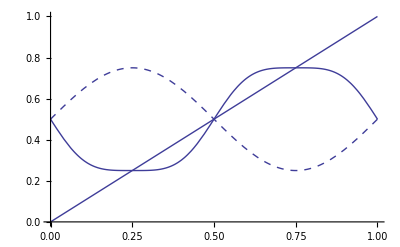

{ϕ→0.25}

```mathematica
Show[Plot[ϕ,{ϕ,0,1}],Plot[f[f[ϕ]]/.α->0.25,{ϕ,0,1},PlotStyle->Thick],Plot[(f[ϕ]/.α->0.25),{ϕ,0,1},PlotStyle->Dashed]]
FindRoot[ϕ == (f[f[ϕ]]/.α->0.25),{ϕ,0.2}]
```

### Exercise 5: The game of life

The game of life is a cellular automaton model suggested by John Conway in 1970 (A good introduction of this famous model can be found at : http://www.math.com/students/wonders/life/life.html). Each cell in a two - dimensional square lattice can be 0 (dead) or 1 (alive). If we define the neighbourhood of each cell as its 8 nearest neighbours (i.e., Moore neighbourhood,   see http://cell-auto.com/neighbourhood/moore/ )
and the updating rules are :
(a) A dead cell surrounded by exactly 3 living cells comes back to life;
(b) A living cell surrounded by < 2 or > 3 living cells will die of isolation or overcrowdness. 
(c) In all the other cases, the cell will remain its state.

Your task is  (i) to fill in the missing codes in the folowing Mathematica program to simulate the evolution of this model. In this program, we begin with an initial condition of placing a R-pentomino in the center of the lattice. 
Try some other initial conditions (e.g., oscillators or gliders, see http://www.math.com/students/wonders/life/life.html ) and run the program. 
(ii) (optional)  If you look at this program carefully, you will find that it has not taken consideration of the four boundaries. So try to devise a way to simulate the game of life aotomaton with periodic boundaries and rewrite the codes.